```mathematica
SetOptions[Plot, AspectRatio -> Automatic]; rucat
tf := TableForm; tx := TeXForm; hh := Hold; 
  ss := Simplify; 
tt[x_] :=TraditionalForm[x]; 
  mf := MatrixForm;
```

rucat

```mathematica
ru1:={"a"->"a","c"->"d","b"->"c","d"->"a","e"->"d","f"->"e","g"->"b","h"->"d","i"->"h","j"->"e"}
```

```mathematica
ru1
```

{a→a,c→d,b→c,d→a,e→d,f→e,g→b,h→d,i→h,j→e}

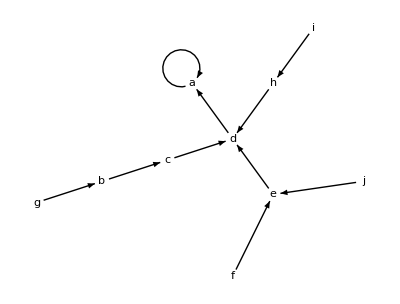

```mathematica
GraphPlot[ru1,VertexLabeling->True, DirectedEdges->True,EdgeRenderingFunction->(Arrow[#1,0.1]&),PlotStyle->Directive[Arrowheads[0.03]],VertexRenderingFunction->(Text[#2,#1]&)]
```

```mathematica
ff["a"]:="a";ff["c"]:="d";ff["b"]:="c";ff["d"]:="a";ff["e"]:="d";ff["f"]:="e";ff["g"]:="b";ff["h"]:="d";ff["i"]:="h";ff["j"]:="e";
```

```mathematica
graph1:=GraphPlot[ru1,VertexLabeling->True, DirectedEdges->True,EdgeRenderingFunction->(Arrow[#1,0.1]&),PlotStyle->Directive[Arrowheads[0.03]],VertexRenderingFunction->(Text[#2,#1]&)]
```

```mathematica
Remove[graphname]
```

```mathematica
Export["C:\\Documents and Settings\\All Users\\Documents\\Data\\New Ab Math\\AbMath in TeX\\AbMath Mathematica\\graph1.pdf",graph1]
```

Export::nodir: Directory C:\Documents and Settings\All Users\Documents\Data\New Ab Math\AbMath in TeX\AbMath Mathematica\ does not exist.

Export::noopen: Cannot open C:\Documents and Settings\All Users\Documents\Data\New Ab Math\AbMath in TeX\AbMath Mathematica\graph1.pdf.

$Failed

```mathematica
graphname:="C:\\Documents and Settings\\All Users\\Documents\\Data\\New Ab Math\\AbMath in TeX\\AbMath Mathematica\\graph101.pdf"
```

```mathematica
Export[graphname,"graph1.pdf"]
```

Export::nodir: Directory C:\Documents and Settings\All Users\Documents\Data\New Ab Math\AbMath in TeX\AbMath Mathematica\ does not exist.

Export::noopen: Cannot open C:\Documents and Settings\All Users\Documents\Data\New Ab Math\AbMath in TeX\AbMath Mathematica\graph101.pdf.

$Failed

```mathematica
ru2:=#->ff[#]&/@{"a","b","c","d","e","f","g","h","i","j"}
```

```mathematica
GraphPlot[ru2,VertexLabeling->True, DirectedEdges->True,EdgeRenderingFunction->(Arrow[#1,0.1]&),PlotStyle->Directive[Arrowheads[0.03]],VertexRenderingFunction->(Text[#2,#1]&)]
```

-Graphics-

```mathematica
ru3:=#->ff[ff[#]]&/@{"a","b","c","d","e","f","g","h","i","j"}
```

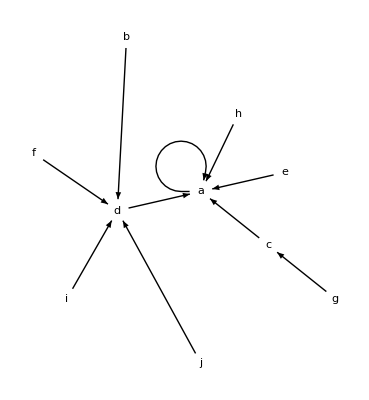

```mathematica
GraphPlot[ru3,VertexLabeling->True, DirectedEdges->True,EdgeRenderingFunction->(Arrow[#1,0.1]&),PlotStyle->Directive[Arrowheads[0.02]],VertexRenderingFunction->(Text[#2,#1]&)]
```

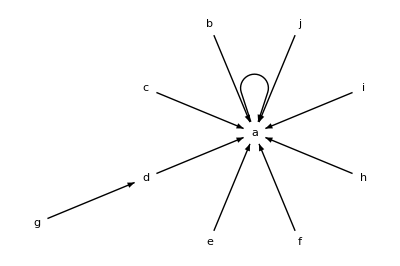

```mathematica
GraphPlot[#->ff[ff[ff[#]]]&/@{"a","b","c","d","e","f","g","h","i","j"},VertexLabeling->True, DirectedEdges->True,EdgeRenderingFunction->(Arrow[#1,0.1]&),PlotStyle->Directive[Arrowheads[0.02]],VertexRenderingFunction->(Text[#2,#1]&)]
```

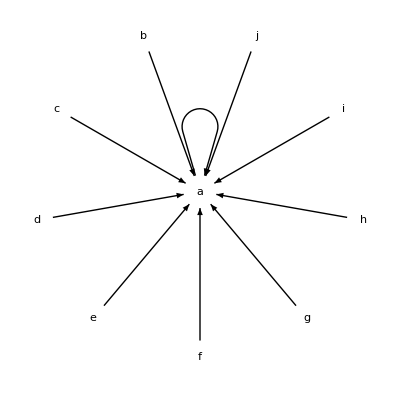

```mathematica
GraphPlot[#->ff[ff[ff[ff[#]]]]&/@{"a","b","c","d","e","f","g","h","i","j"},VertexLabeling->True, DirectedEdges->True,EdgeRenderingFunction->(Arrow[#1,0.1]&),PlotStyle->Directive[Arrowheads[0.02]],VertexRenderingFunction->(Text[#2,#1]&)]
```

```mathematica
FunctionGraph[r_]:=GraphPlot[r,VertexLabeling->True, DirectedEdges->True,EdgeRenderingFunction->(Arrow[#1,0.1]&),PlotStyle->Directive[Arrowheads[0.03]],VertexRenderingFunction->(Text[#2,#1]&)]
```

```mathematica
FunctionGraph[ru1]
```

-Graphics-

```mathematica
MakeRule[f_,l_]:=#->f[#]&/@l
```

```mathematica
g[n_]:=Mod[n^2+1,11]
```

```mathematica
Remove[f]
```

```mathematica
MakeFunctionRule[f_,n_]:=#->f[#]&/@ Table[k,{k,0,n-1}]
```

```mathematica
MakeFunctionRule[g,13]
```

{0→1,1→2,2→5,3→10,4→6,5→4,6→4,7→6,8→10,9→5,10→2,11→1,12→2}

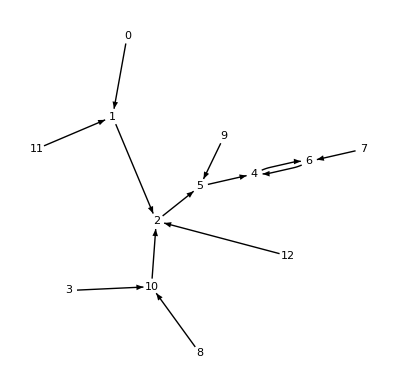

```mathematica
FunctionGraph[MakeFunctionRule[g,13]]
```

```mathematica
h[n_]:=Mod[n^9,11]
```

```mathematica
MakeFunctionRule[h,11]
```

{0→0,1→1,2→6,3→4,4→3,5→9,6→2,7→8,8→7,9→5,10→10}

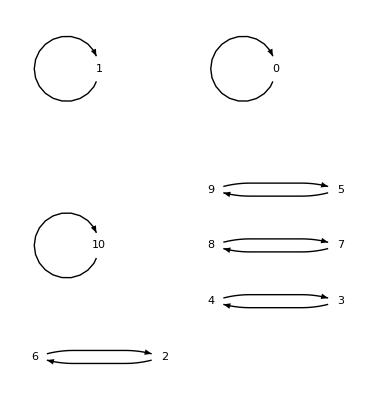

```mathematica
FunctionGraph[MakeFunctionRule[h,11]]
```

```mathematica
Remove[fg]
```

```mathematica
fg[x_,n_]:=FunctionGraph[MakeFunctionRule[x,n]]
```

```mathematica
k[n_]:=Mod[n^9+n^7+5n,11]
```

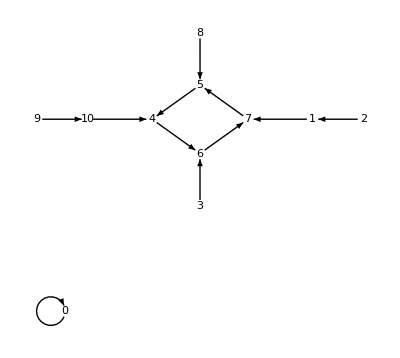

```mathematica
fg[k,11]
```

```mathematica
s[n_]:=Mod[(n+1)^9+n^7+5n,11]
```

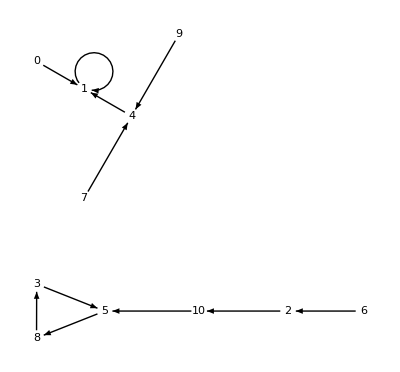

```mathematica
fg[s,11]
```

```mathematica
aaa[n_]:=Mod[(n+1)^9+(n^+2)^7+5n,11]
```

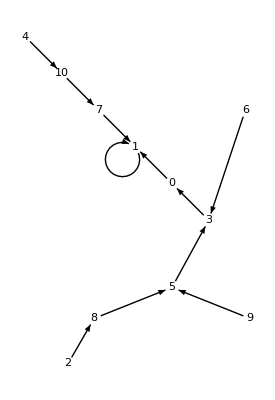

```mathematica
fg[aaa,11]
```

```mathematica
bbb[n_]:=Mod[n^2+5,11]
```

```mathematica
fg[bbb.11]
```

fg[0.11 bbb]

```mathematica
ccc[n_]:=Mod[n^3+5,11]
```

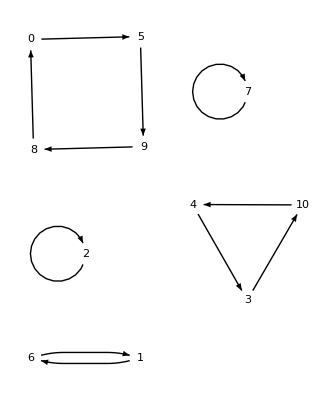

```mathematica
fg[ccc,11]
```

```mathematica
ddd[n_]:=Mod[n^3+n^2,11]
```

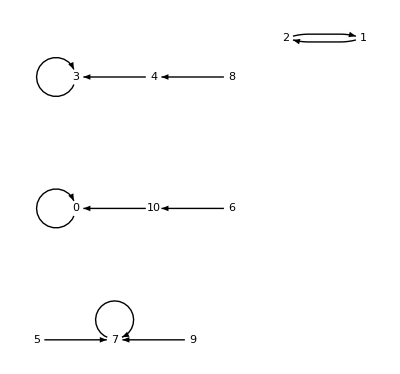

```mathematica
fg[ddd,11]
```

```mathematica
Remove[g]
```

```mathematica
g[n_]:=Mod[n^2+1,11]
```

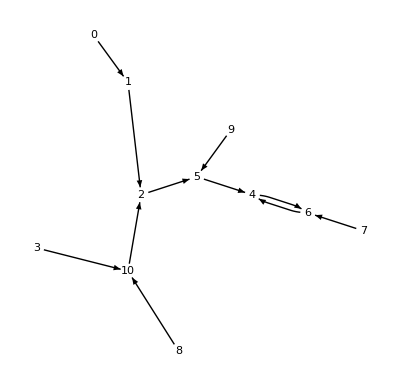

```mathematica
fg[g,11]
```

```mathematica
gg[x_]:=g[g[x]]
```

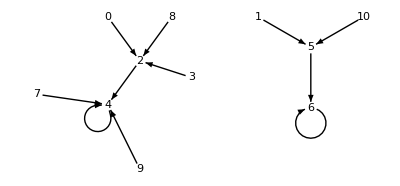

```mathematica
fg[gg,11]
```

```mathematica
ggg[x_]:=g[g[g[x]]]
```

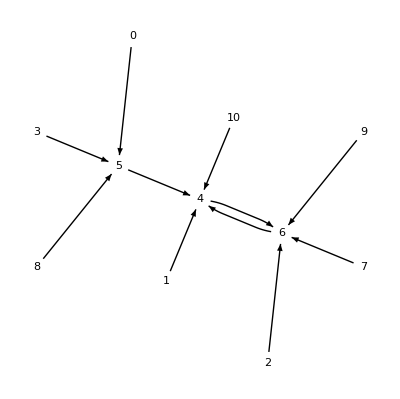

```mathematica
fg[ggg,11]
```

```mathematica
ht[n_]:=Mod[n^(11),13]
```

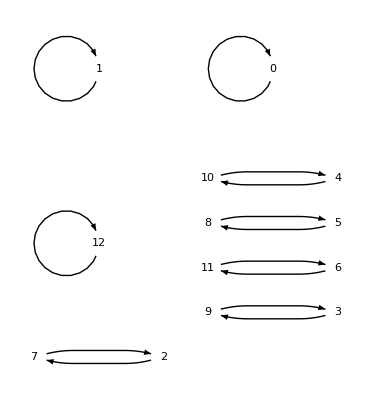

```mathematica
fg[ht,13]
```

```mathematica
htx[n_]:=Mod[n^(11)+n^9+n^7+1,13]
```

```mathematica
htx[11]
```

4

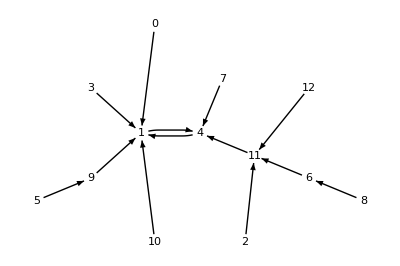

```mathematica
fg[htx,13]
```

```mathematica
Table[{n,htx[n]},{n,0,12}]//tf
```

0 | 1
1 | 4
2 | 11
3 | 1
4 | 1
5 | 9
6 | 11
7 | 4
8 | 6
9 | 1
10 | 1
11 | 4
12 | 11

```mathematica
fbig[0]:=5;fbig[1]:=2;fbig[2]:=13;fbig[3]:=4;fbig[4]=14;fbig[5]:=6;fbig[6]:=7;fbig[7]:=8;fbig[8]:=9;fbig[9]:=10;fbig[10]:=5;fbig[11]:=2;fbig[12]:=2;fbig[13]:=14;fbig[14]:=7;
```

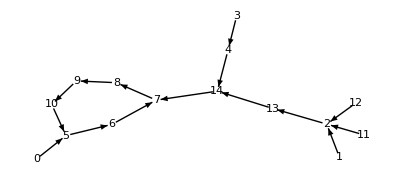

```mathematica
fg[fbig,15]
```

```mathematica
fgc[x_,y_,n_]:=Show[fg[x,n],fg[y,n]]
```

```mathematica
hdem[n_]:=Mod[n^2+5,15]
```

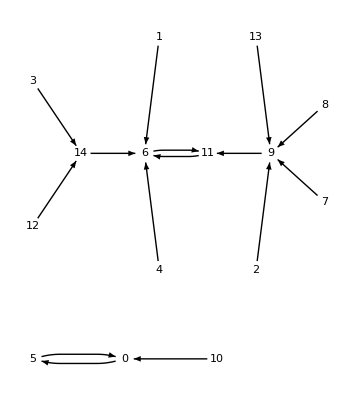

```mathematica
fg[hdem,15]
```

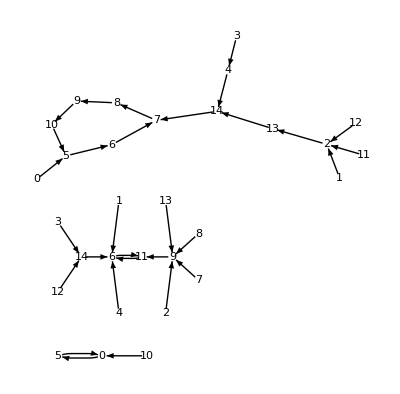

```mathematica
fgc[fbig,hdem,15]
```